```mathematica
(* Notation:
ep, em; fp, fm = number of each type of electron up/down (e = ej and f = ei)
np, nm = number of nuclei up/down
et, ft, nt = total number of each electron/nuclei *)
```

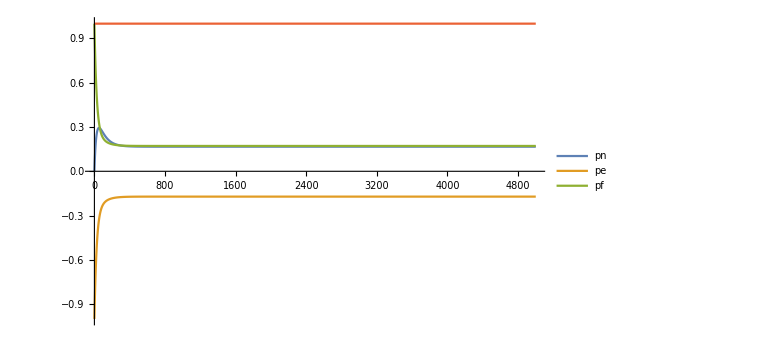

```mathematica
(* A thermal mixing model with more parameters *)
ClearAll["Global`*"];
(* Parameters to change:
 Below, you can change the value of the rates a and b.
* peInit, pfInit, and pnInit are the initial polarizations of the two types of electrons and the nuclei, respectively.
* ce and cf are the ratios of the number of each type of electron to the number of nuclei (the analogue to the constant C in the solid effect).
*)
(* Description of rate parameters:
Spin up/down is indicated by + or -; the states listed give the spins of electrons e, electrons f, and nuclei (in that order).
Pumping parameters are represented by ↔, while relaxation rates are represented by ->.
* a: +-+ ↔ -+-
* b: +-- ↔ -++
* q: --+ -> --- and +++ -> ++- (probably either useless or non-physical)
* r: +++ -> --+ and ++- -> --- (does not yield physical results)
* u: +-+ -> -+- and +-- -> -++ (similar to σ in Jeffries)
* v: +-+ -> -++ and +-- -> -+- (set this equal to 1, probably)
* w: +-+ -> +-- and -++ -> -+- (similar to θ in Jeffries)
*)
subs={nt->np[t]+nm[t],et->ep[t]+em[t],ft->fp[t]+fm[t]};
assumptions={v->1,q->0,r->0,u->0};
rates={ω1->0.005,a->5,b->1,w->1};
allRates=assumptions∪rates;
initial={peInit->-1,pfInit->1,pnInit->0};
constants={t1e->0.05,t1n->25*60,pe0->-1,pf0->0,pn0->0,ce->1,cf->1};
totalTime=5000;
epDot=cf/(ft nt)(-ep[t]fp[t]np[t](r(1-pe0-pf0))
-ep[t]fp[t]nm[t](r(1-pe0-pf0))
-ep[t] fm[t]np[t](a+u(1-pe0+pf0-pn0)+v(1-pe0+pf0))
-ep[t]fm[t]nm[t](b+u(1-pe0+pf0+pn0)+v(1-pe0+pf0))
+em[t] fp[t]np[t](b+u(1+pe0-pf0-pn0)+v(1+pe0-pf0))
+em[t] fp[t]nm[t](a+u(1+pe0-pf0)+v(1+pe0-pf0))
+em[t]fm[t]np[t](r(1+pe0+pf0))
+em[t]fm[t]nm[t](r(1+pe0+pf0)))ω1;
emDot=-epDot;
fpDot=ce/(et nt)(-fp[t]ep[t]np[t](r(1-pe0-pf0))
-fp[t]ep[t]nm[t](r(1-pe0-pf0))
-fp[t] em[t]np[t](b+u(1+pe0-pf0-pn0)+v(1+pe0-pf0))
-fp[t] em[t]nm[t](a+u(1+pe0-pf0+pn0)+v(1+pe0-pf0))
+fm[t] ep[t]np[t](a+u(1-pe0+pf0-pn0)+v(1-pe0+pf0))
+fm[t]ep[t]nm[t](b+u(1-pe0+pf0+pn0)+v(1-pe0+pf0))
+fm[t]em[t]np[t](r(1+pe0+pf0))
+fm[t]em[t]nm[t](r(1+pe0+pf0)))ω1;
fmDot=-fpDot;
npDot=ce/(et ft)(-np[t]ep[t]fp[t](q(1-pn0))
-np[t]ep[t]fm[t](a+u(1-pe0+pf0-pn0)+w(1-pn0))
-np[t]em[t]fp[t](b+u(1+pe0-pf0-pn0)+w(1-pn0))
-np[t]em[t]fm[t](q(1-pn0))
+nm[t]ep[t]fp[t](q(1+pn0))
+nm[t]ep[t]fm[t](b+u(1-pe0+pf0+pn0)+w(1+pn0))
+nm[t]em[t]fp[t](a+u(1+pe0-pf0+pn0)+w(1+pn0))
+nm[t]em[t]fm[t](q(1+pn0)))ω1;
nmDot=-npDot;
(* Set up the differential equations *)
thermalMixingEqns={ep'[t]==epDot,
em'[t]==emDot,
fp'[t]==fpDot,
fm'[t]==fmDot,
np'[t]==npDot,
nm'[t]==nmDot,
ep[0]==(ce(1+peInit))/2,em[0]==(ce(1-peInit))/2,
fp[0]==(cf(1+pfInit))/2,fm[0]==(cf(1-pfInit))/2,
np[0]==(1+pnInit)/2,nm[0]==(1-pnInit)/2};
(* Convenient expressions for polarization *)
polSubs={pn->(np[t]-nm[t])/(np[t]+nm[t]),
pe->(ep[t]-em[t])/(ep[t]+em[t]),
pf->(fp[t]-fm[t])/(fp[t]+fm[t]),
nTotal->np[t]+nm[t]};
sol=NDSolve[thermalMixingEqns/.subs/.initial/.allRates/.constants,{em,ep,fm,fp,nm,np},{t,0,totalTime}];
Plot[{pn/.polSubs/.sol,pe/.polSubs/.sol,pf/.polSubs/.sol,nTotal/.polSubs/.sol},{t,0,totalTime},PlotRange->Full,PlotLegends->{"pn","pe","pf"},ImageSize->Large]
```

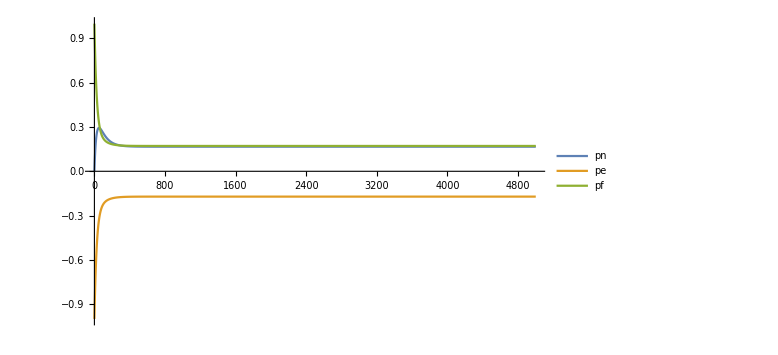

```mathematica
(* Get expressions for Subscript[P, n], etc. by defining them and eliminating np, nm, etc. *)
peExpr=(ep[t]-em[t])/et/.subs;
pfExpr=(fp[t]-fm[t])/ft/.subs;
pnExpr=(np[t]-nm[t])/nt/.subs;
fnSubs={pn->pn[t],pe->pe[t],pf->pf[t]};
pnDotEqn=pnDot/.Solve[Eliminate[{pnDot==(npDot-nmDot)/nt/.subs,
pn==pnExpr,pe==peExpr,pf==pfExpr},
{np[t],nm[t],ep[t],em[t],fp[t],fm[t]}],pnDot][[1]]/.fnSubs;
peDotEqn=peDot/.Solve[Eliminate[{peDot==(epDot-emDot)/et/.subs,
pn==pnExpr,pe==peExpr,pf==pfExpr},
{np[t],nm[t],ep[t],em[t],fp[t],fm[t]}],peDot][[1]]/.fnSubs;
pfDotEqn=pfDot/.Solve[Eliminate[{pfDot==(fpDot-fmDot)/ft/.subs,
pn==pnExpr,pe==peExpr,pf==pfExpr},
{np[t],nm[t],ep[t],em[t],fp[t],fm[t]}],pfDot][[1]]/.fnSubs;
polSolution=NDSolve[{pn'[t]==pnDotEqn,pe'[t]==peDotEqn,pf'[t]==pfDotEqn,pn[0]==pnInit,pe[0]==peInit,pf[0]==pfInit}/.initial/.allRates/.constants,{pn,pe,pf},{t,0,totalTime}];
Plot[{pn[t]/.polSolution,pe[t]/.polSolution,pf[t]/.polSolution},{t,0,totalTime},PlotRange->Full,PlotLegends->{"pn","pe","pf"},ImageSize->Large]
```

```mathematica
relaxationModel={pn'[t]==pnDotEqn,pe'[t]==peDotEqn,pf'[t]==pfDotEqn,
pn[0]==pnInit,pe[0]==peInit,pf[0]==pfInit}/.{a->0,b->0,q->0,r->0,v->1,u->0,pe0->-1,pf0->0,pn0->0}//Simplify;
solution=DSolve[relaxationModel[[1;;3]],{pn,pe,pf},t][[1]]//Simplify;
{pn[0]==pnInit,pe[0]==-1,pf[0]==1}/.solution
(* Things I deduced from this model:
* Just as one of the relaxation rates in the solid effect is set to 1, I propose that v should always be 1(this makes the Subscript[T, 1e] expression come out nicely, providing a good interpretation for ω1)
* Also, r seems to be pretty useless, so set it to 0 for now.
* Same for q; it doesn't seem like it makes any difference.
* With this assumption, we get the values for Subscript[T, 1e] and Subscript[T, 1n] described below. However, the behavior of Subscript[P, n] is not quite the single exponential as we would expect, but it asymptotically approaches this form, allowing for an asymptotic Subscript[T, 1n].
*)
```

{ⅇ^(-(ce w ω1 ((cf ⅇ^(cf C[2]) (ce (-4+C[1])+cf (-1+C[1]) C[1]))/((-ce ⅇ^(cf C[2])+ⅇ^((ce+cf C[1]) C[2])) ω1 (ce+cf (-1+C[1])))+(ⅇ^((ce+cf C[1]) C[2]) (ce^2-cf^2 (-1+C[1])+ce cf (2+C[1])))/(ce (-ce ⅇ^(cf C[2])+ⅇ^((ce+cf C[1]) C[2])) ω1 (ce+cf (-1+C[1])))-((ce+cf) Log[-ce ⅇ^(cf C[2])+ⅇ^((ce+cf C[1]) C[2])])/(ce ω1)))/cf) C[3]==pnInit,(cf ⅇ^(cf C[2])-ⅇ^(ce C[2]+cf C[1] C[2])-cf ⅇ^(cf C[2]) C[1])/(-ce ⅇ^(cf C[2])+ⅇ^(ce C[2]+cf C[1] C[2]))==-1,C[1]-(ce (cf ⅇ^(cf C[2])-ⅇ^(ce C[2]+cf C[1] C[2])-cf ⅇ^(cf C[2]) C[1]))/(cf (-ce ⅇ^(cf C[2])+ⅇ^(ce C[2]+cf C[1] C[2])))==1}

```mathematica
conditions={pn[0]==pnInit,pe[0]==-1,pf[0]==1}/.solution;
conditions[[1]]
Solve[conditions[[2]],C[3]]
```

ⅇ^(-(ce w ω1 ((cf ⅇ^(cf C[2]) (ce (-4+C[1])+cf (-1+C[1]) C[1]))/((-ce ⅇ^(cf C[2])+ⅇ^((ce+cf C[1]) C[2])) ω1 (ce+cf (-1+C[1])))+(ⅇ^((ce+cf C[1]) C[2]) (ce^2-cf^2 (-1+C[1])+ce cf (2+C[1])))/(ce (-ce ⅇ^(cf C[2])+ⅇ^((ce+cf C[1]) C[2])) ω1 (ce+cf (-1+C[1])))-((ce+cf) Log[-ce ⅇ^(cf C[2])+ⅇ^((ce+cf C[1]) C[2])])/(ce ω1)))/cf) C[3]==pnInit

{{}}

```mathematica
(* Expression for Subscript[T, 1e]^-1 *)
t1eExpr=1/((ce+cf)(u+v)ω1);
Print["T_(1  e) = ",t1eExpr]
(* Expression for Subscript[T, 1n]^-1 *)
t1nExpr=(2(ce+cf)^2(u+v))/(8ce cf(ce+cf)(u+v)(u+w)ω1)//Simplify;
Print["T_(1  n) = ",t1nExpr]
```

T_(1  e) = 1/((ce+cf) (u+v) ω1)

T_(1  n) = (ce+cf)/(4 ce cf u ω1+4 ce cf w ω1)

```mathematica
(* Get the model above to use Subscript[T, 1n] and Subscript[T, 1e] instead of ω1 and w *)
(* We will also make the assumptions: v = 1, q = 0, r = 0, pn0 = 0, Subscript[P, e](0) = -1, and Subscript[P, f](0) = 1 *)
omega1Expr=ω1/.Solve[t1e==t1eExpr,ω1][[1]];
wExpr=w/.Solve[t1n==t1nExpr,w][[1]]/.{ω1->omega1Expr};
t1Subs={ω1->omega1Expr,w->wExpr};
pnDotNew=pnDotEqn/.t1Subs/.assumptions//FullSimplify;
peDotNew=peDotEqn/.t1Subs/.assumptions//FullSimplify;
pfDotNew=pfDotEqn/.t1Subs/.assumptions//FullSimplify;
Print["P_n' = ",pnDotNew]
Print["P_e' = ",peDotNew]
Print["P_f' = ",pfDotNew]
```

P_n' = 1/(4 cf (ce+cf) t1e t1n)((ce+cf)^2 pn0 t1e+2 (a-b) ce cf t1n pf[t]-((ce+cf)^2 t1e+2 (a+b) ce cf t1n) pn[t]+pe[t] (2 (-a+b) ce cf t1n+pf[t] (-(ce+cf)^2 pn0 t1e+((ce+cf)^2 t1e+2 (a+b) ce cf t1n) pn[t])))

P_e' = -(cf (-2 pe0+2 pf0-(2+a+b) pf[t]+(a-b) pn[t]+pe[t] (2+a+b+pf[t] (2 pe0-2 pf0-a pn[t]+b pn[t]))))/(2 (ce+cf) t1e)

P_f' = (ce (-2 pe0+2 pf0-(2+a+b) pf[t]+(a-b) pn[t]+pe[t] (2+a+b+pf[t] (2 pe0-2 pf0-a pn[t]+b pn[t]))))/(2 (ce+cf) t1e)

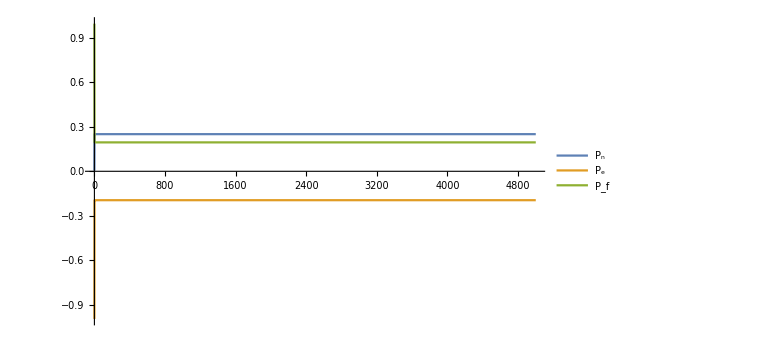

```mathematica
polSol=NDSolve[{pn'[t]==pnDotNew,pe'[t]==peDotNew,pf'[t]==pfDotNew,
pn[0]==pnInit,pe[0]==peInit,pf[0]==pfInit}/.constants/.rates/.initial,{pn,pe,pf},{t,0,totalTime}];
Plot[{pn[t]/.polSol,pe[t]/.polSol,pf[t]/.polSol},{t,0,totalTime},PlotRange->Full,ImageSize->Large,PlotLegends->{"P_n","P_e","P_f"}]
```

```mathematica
{pn'[t]==pnDotEqn,pe'[t]==peDotEqn,pf'[t]==pfDotEqn,
pn[0]==pnInit,pe[0]==peInit,pf[0]==pfInit}/.{peInit->-1,pfInit->1,a->0,b->0,q->0,r->0,v->1,u->0,pe0->-1,pf0->0,pn0->0}
```

{pn'[t]==1/2 (-2 ce w ω1 pn[t]+2 ce w ω1 pe[t] pf[t] pn[t]),pe'[t]==1/4 (-4 cf ω1-4 cf ω1 pe[t]+4 cf ω1 pf[t]+4 cf ω1 pe[t] pf[t]),pf'[t]==1/2 (2 ce ω1+2 ce ω1 pe[t]-2 ce ω1 pf[t]-2 ce ω1 pe[t] pf[t]),pn[0]==pnInit,pe[0]==-1,pf[0]==1}